```mathematica
SolutionTreeGraph[h_]:=Block[
{edges=Map[EdgeList[PathGraph[Map[ToString[#]&,Haccumulate[ RecordToCouples[#]]]]]&,ToVarsLogical[h,x1==1]]},
With[
{g=Graph[DeleteDuplicates[Flatten[edges]]]},
Graph[g, GraphLayout->"RadialDrawing",VertexStyle->Map[#->IndexToColor[ FromDigits[ StringTake[#,-1]]]&, VertexList[g]], PlotLabel->{ChromaticPolynomial[h,4]/24,GraphSignature2[h]}
]
]
]
```

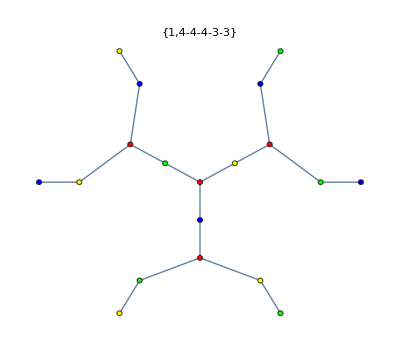
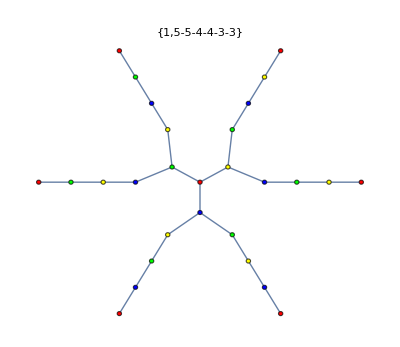
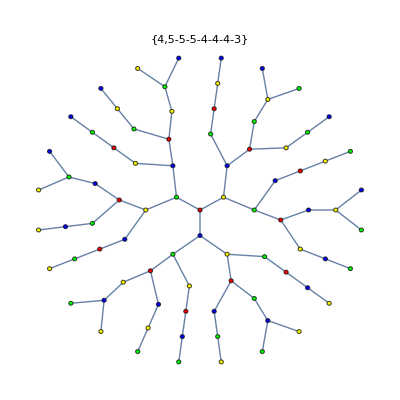
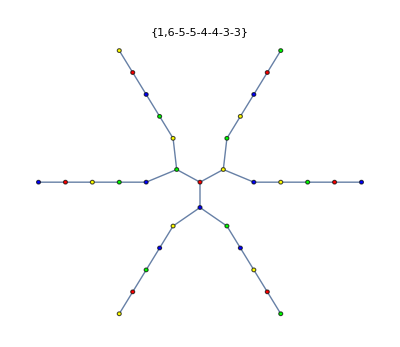
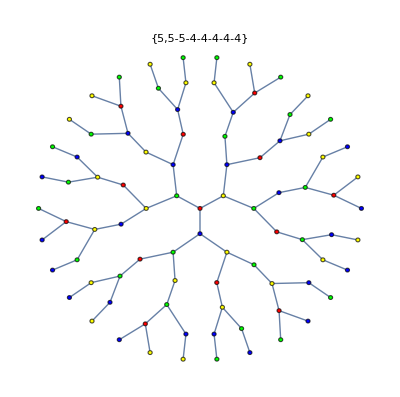
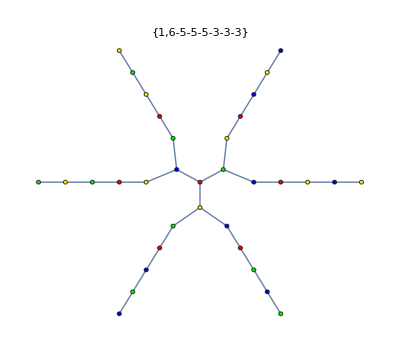
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-

```mathematica
TableForm[Table[
SolutionTreeGraph[ReadGrof[deps3[[k,1]]]]->SolutionTreeGraph[ReadGrof[deps3[[k,2]]]],{k,1,5}]]
```

```mathematica
Take[deps1,3]
```

{{0,1,{1,{1,2,3}}},{1,2,{1,{1,2,4}}},{2,3,{1,{2,3,4}}}}

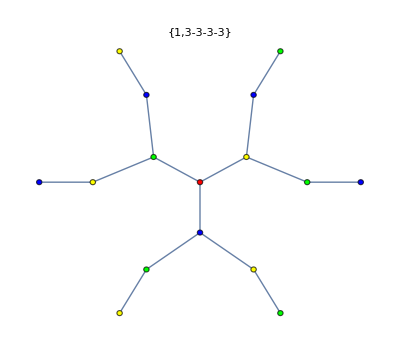
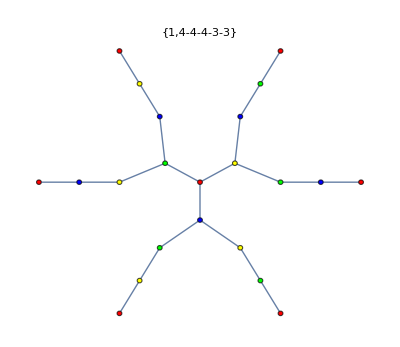
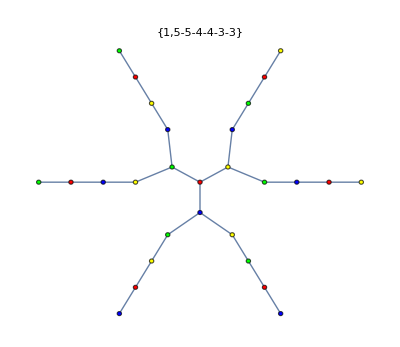
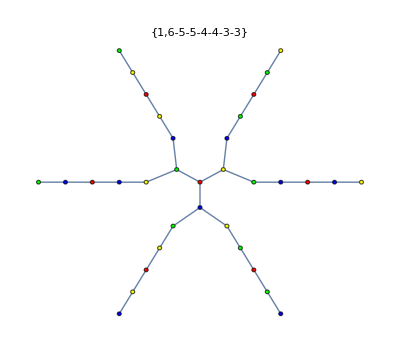
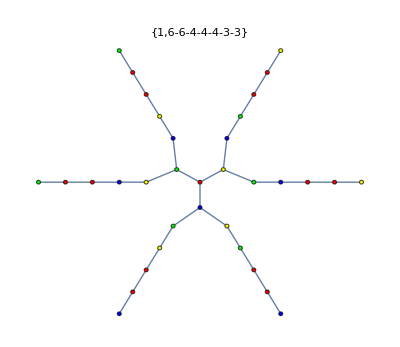
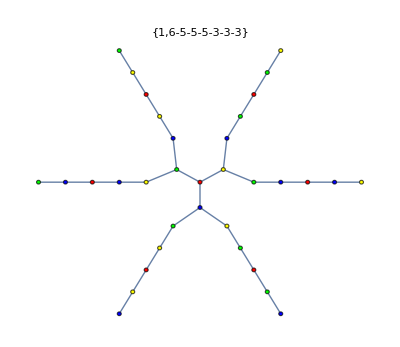
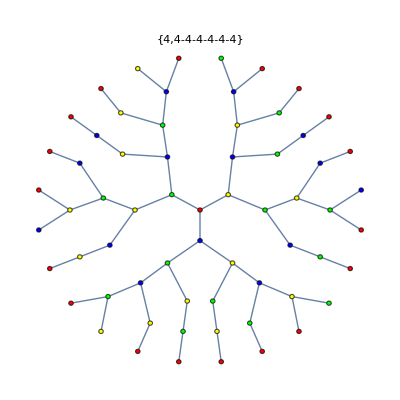
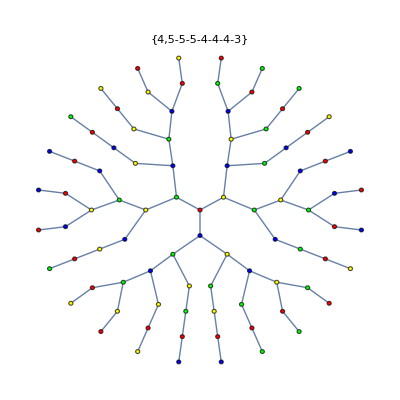
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-

```mathematica
TableForm[Table[
SolutionTreeGraph[ReadGrof[deps1[[k,1]]]]->SolutionTreeGraph[ReadGrof[deps1[[k,2]]]],{k,2,10}]]
```

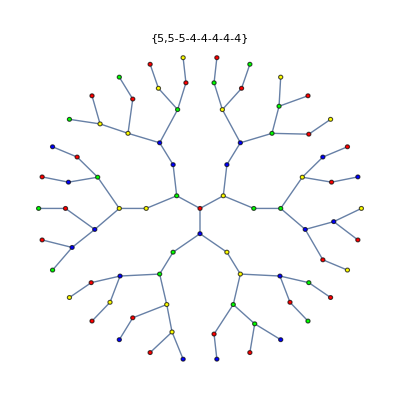
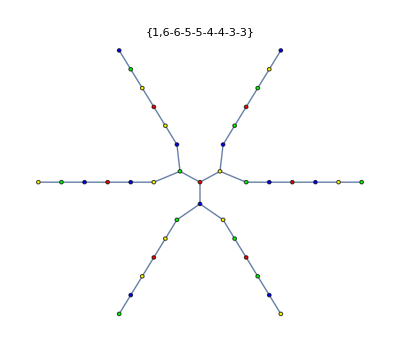
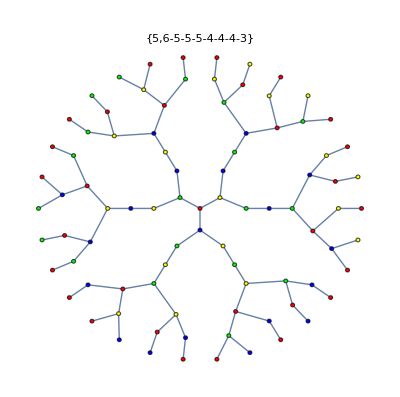
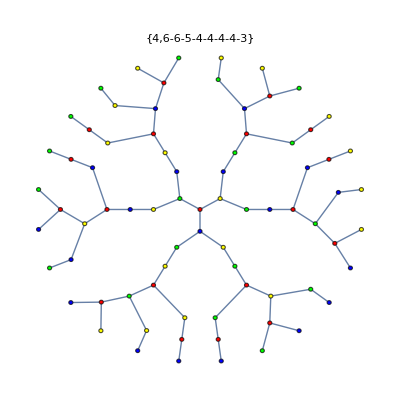
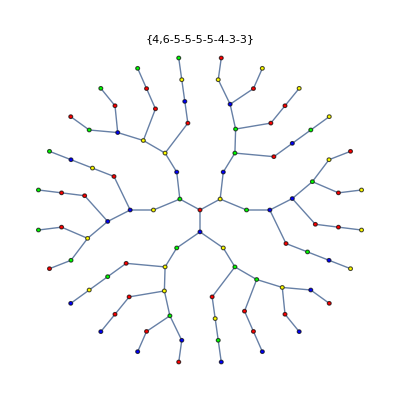
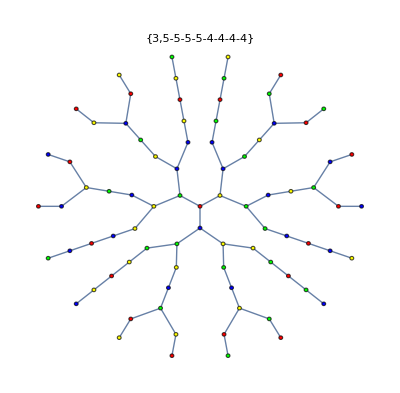
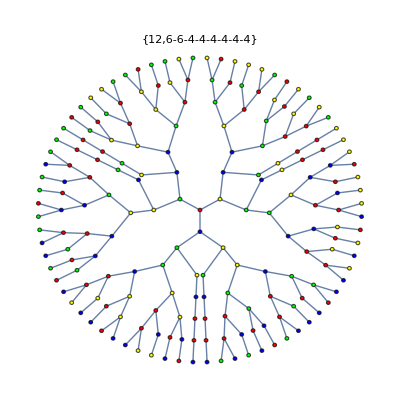
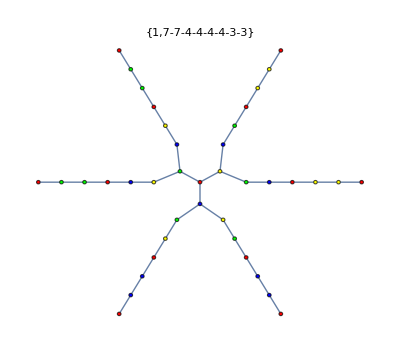
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-

```mathematica
TableForm[Table[
SolutionTreeGraph[ReadGrof[deps2[[k,1]]]]->SolutionTreeGraph[ReadGrof[deps2[[k,2]]]],{k,2,50}]]
```